```mathematica
SKRules={k[x_][y_]:> x,s[x_][y_][z_]:> x[z][y[z]]};
SKEvaluate[expr_]:=
NestList[#1/.SKRules&,expr,50];
```

```mathematica
SKEvaluate[s[x[a]][y[b]][z[c]]]
```

{s[x[a]][y[b]][z[c]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]],x[a][z[c]][y[b][z[c]]]}

```mathematica
ClearAll[a,b,c,x,y,z,s,k]
```

```mathematica
t = Table[x->RandomChoice[{"s","k"}]<>ToString[x],{x,0,10}]
```

{0→k0,1→k1,2→k2,3→s3,4→s4,5→s5,6→s6,7→s7,8→k8,9→k9,10→s10}

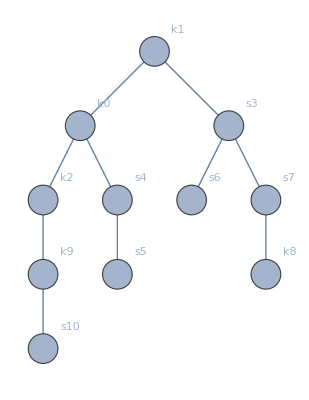

```mathematica
g=TreeGraph[RandomInteger[#]<->#+1&/@Range[0,9],VertexSize->0.4,VertexLabels->t]
```

```mathematica
DepthFirstScan[g,0, {"PrevisitVertex" -> (Print["Visiting ", #," ",t[[#+1]]] &),"FrontierEdge" -> (Print["FrontierEdge",#,##]&),"BackEdge" -> (Print["BackEdge",#,##]&),"ForwardEdge" -> (Print["ForwardEdge",#,##]&),"CrossEdge" -> (Print["CrossEdge",#,##]&)}];
```

Visiting 0 0→k0

FrontierEdge0<->10<->1

Visiting 1 1→k1

BackEdge1<->01<->0

FrontierEdge1<->31<->3

Visiting 3 3→s3

BackEdge3<->13<->1

FrontierEdge3<->63<->6

Visiting 6 6→s6

BackEdge6<->36<->3

FrontierEdge3<->73<->7

Visiting 7 7→s7

BackEdge7<->37<->3

FrontierEdge7<->87<->8

Visiting 8 8→k8

BackEdge8<->78<->7

FrontierEdge0<->20<->2

Visiting 2 2→k2

BackEdge2<->02<->0

FrontierEdge2<->92<->9

Visiting 9 9→k9

BackEdge9<->29<->2

FrontierEdge9<->109<->10

Visiting 10 10→s10

BackEdge10<->910<->9

FrontierEdge0<->40<->4

Visiting 4 4→s4

BackEdge4<->04<->0

FrontierEdge4<->54<->5

Visiting 5 5→s5

BackEdge5<->45<->4

```mathematica
RandomSKGraph[n_]:=Module[{t,g},
t = Table[x->RandomChoice[{"s","k"}]<>ToString[x],{x,0,n-1}];
g=TreeGraph[RandomInteger[#]-> #+1&/@Range[0,n-2],VertexSize->0.4,VertexLabels->t]
]
```

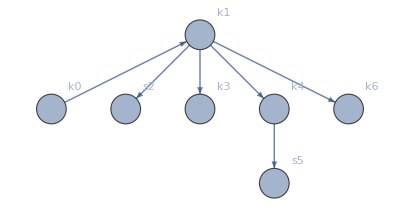

```mathematica
RandomSKGraph[7]
```

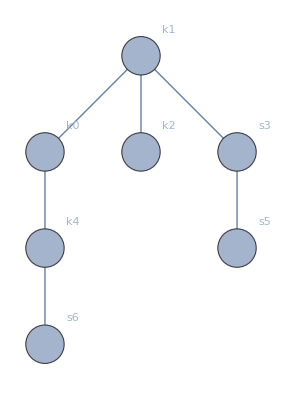
```mathematica
DepthFirstScan[-Graphics-,0, {"PrevisitVertex" -> (Print["Visiting ", #," ",t[[#+1]]] &),"FrontierEdge" -> (Print["FrontierEdge",#]&),"BackEdge" -> (Print["BackEdge",#]&),"ForwardEdge" -> (Print["ForwardEdge",#]&),"CrossEdge" -> (Print["CrossEdge",#]&),"DiscoverVertex" -> (Print["DiscoverVertex",#]&),"UnvisitedVertex" -> (Print["UnvisitedVertex",#]&),"VisitedVertex" -> (Print["VisitedVertex",#]&)}];
```

```mathematica
g2 = -Graphics-
```

-Graphics-

```mathematica
g2[[0]]
```

Graph

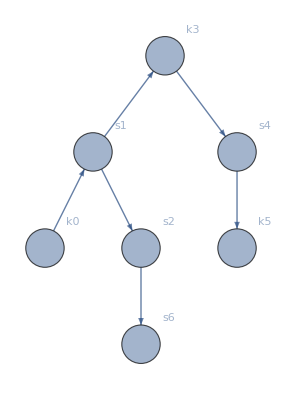

```mathematica
k=RandomSKGraph[7]
```

```mathematica
Leaves[graph_,x_]:=Rest[VertexOutComponent[graph,x,1]]
```

```mathematica
Leaves[k,1]
```

{2,3}

```mathematica
VertexOutComponent[k,1,1]
```

{1,2,3}

```mathematica
AdjacencyList[%83]
```

{{1,2,4},{0},{0},{0}}

```mathematica
ClearAll[k]
```

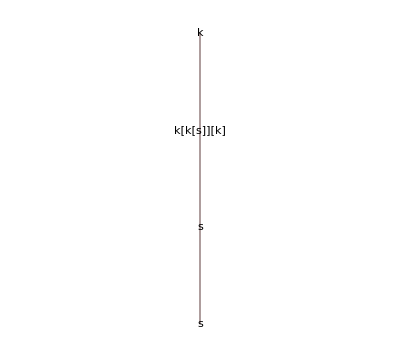

```mathematica
k[k[k[s]][k][s[s]]]//TreeForm
```

```mathematica
RandomSKExpr[0,current_]:=current;
```

```mathematica
RandomSKExpr[0,current_]:=current;
RandomSKExpr[depth_,current_]:= 
RandomSKExpr[depth-1,
RandomChoice[{
RandomChoice[{s,k}][current],
current[RandomSKExpr[depth-1,RandomChoice[{s,k}]]]
}]
];
RandomSKExpr[depth_Integer]:=RandomSKExpr[depth,RandomChoice[{s,k}]];
```

```mathematica
RandomSKExpr[5]
```

k[k[k[k[s[k[k[k]][s[s]][s]]]]]]

```mathematica
Flatten[Permutations/@IntegerPartitions[5],1]
```

{{5},{4,1},{1,4},{3,2},{2,3},{3,1,1},{1,3,1},{1,1,3},{2,2,1},{2,1,2},{1,2,2},{2,1,1,1},{1,2,1,1},{1,1,2,1},{1,1,1,2},{1,1,1,1,1}}